```mathematica
dir = NotebookDirectory[]<>"../parameterEstimation/fourPopulationModelData/";
```

```mathematica
rawData=Import[dir<>"outputData_params_1_2019-11-18.txt","Data"];
```

```mathematica
header=rawData[[1]]
```

{#(mu,rEff0,Gamma_E,Gamma_B,alpha_1,alpha_2)}

```mathematica
params=rawData[[2;;]];
```

```mathematica
ListPlot3D[{params[[#,2]],params[[#,5]],params[[#,6]]}&/@Range[1,Length[params]],
Mesh->None,
InterpolationOrder->3,
ColorFunction->"SouthwestColors",
AxesLabel->{"r_E(0)","α_1","α_2"}
]
```

-Graphics3D-

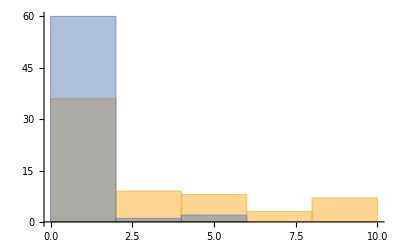

```mathematica
Histogram[{params[[;;,2]],params[[;;,6]]}]
```

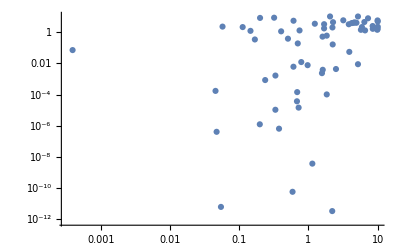

```mathematica
ListLogLogPlot[{params[[#,2]],params[[#,5]]}&/@Range[params//Length]]
```

```mathematica
tooltip2=Cases[DistributionChart[{params[[#,2]]}&/@Range[params//Length]],
Tooltip[_,t_]:>t,All][[1]];
DistributionChart[{rMvals,Tooltip[Rescale[rMsmallvals,{0,0.2},{0,1.2}],tooltip2]},
FrameTicks->{{Automatic,Charting`FindTicks[{0,1.2},{0,0.2}][##&@@{0,1.2}]},{None,None}},
PlotRange->{All,{-0.05,1.2}},
ChartStyle->{Darker[Green],Blue},
FrameStyle->Directive[Thickness[0.0025],Black],
LabelStyle->{Black,FontSize->18,FontFamily->"Arial"},
ImageSize->500
]
```

```mathematica
header
```

{#(mu,rEff0,Gamma_E,Gamma_B,alpha_1,alpha_2)}

```mathematica
nRuns=Length[params];
mu=params[[#,1]]&/@Range[nRuns];
rEff0=params[[#,2]]&/@Range[nRuns];
γE=params[[#,3]]&/@Range[nRuns];
γB=params[[#,4]]&/@Range[nRuns];
α1=params[[#,5]]&/@Range[nRuns];
α2=params[[#,6]]&/@Range[nRuns];
```

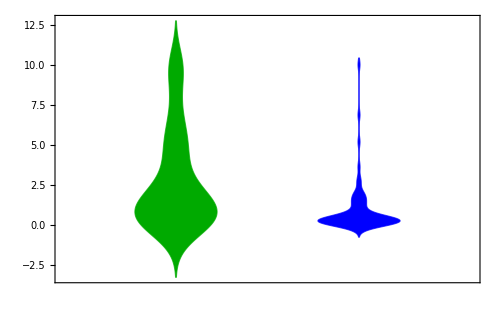

```mathematica
tooltip2=Cases[DistributionChart[{mu}],Tooltip[_,t_]:>t,All][[1]];
DistributionChart[{rEff0,Tooltip[Rescale[mu,MinMax@mu,MinMax@rEff0],tooltip2]},
FrameTicks->{{Automatic,Charting`FindTicks[MinMax@rEff0,MinMax@mu][##&@@MinMax@rEff0]},{None,None}},
ChartStyle->{Darker[Green],Blue},
FrameStyle->Directive[Thickness[0.0025],Black],
LabelStyle->{Black,FontSize->18,FontFamily->"Arial"},
ImageSize->500
]
```

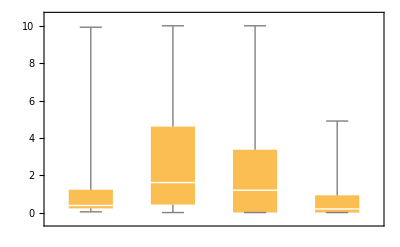

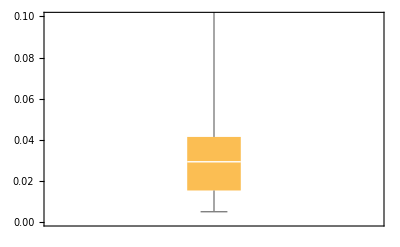

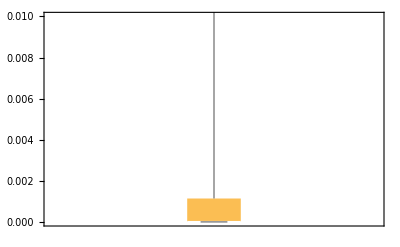

```mathematica
BoxWhiskerChart[{mu,rEff0,α1,α2}]
BoxWhiskerChart[γB,PlotRange->{0,0.1}]
BoxWhiskerChart[γE,PlotRange->{0,0.01}]
```

```mathematica
genQuartiles[var_]:=Quartiles[var];
genQuartiles[#]&/@{rEff0,mu,γE,γB,α1,α2}
```

{{0.428676,1.60634,4.60369},{0.2235,0.378113,1.22077},{7.09049×10^-7,0.0000126581,0.00113839},{0.0152933,0.0292649,0.0413573},{0.00271273,1.19578,3.36349},{0.00028268,0.193605,0.923246}}

```mathematica
dir = NotebookDirectory[]<>"../parameterEstimation/twoPopulationModelData/";
```

```mathematica
rawData=Import[dir<>"outputData_1_2019-11-17.txt","Data"];
paramData=Import[dir<>"outputData_params_1_2019-11-17.dat","Data"];
```

```mathematica
rawData[[7]]
```

[14.095, 6.42, 1.095, 0.21, 0.135]	[6.0, 0.18]	[0.428707, 159.709, 0.0214556, 18.7916]	0.014763128198414983

```mathematica
params=paramData[[2;;]]
```

{{0.368274,131.683,0.0328469,16.6127},{0.413877,159.538,0.02142,18.7752},{0.320677,253.705,8.29671×10^-13,35.2229},{0.375851,131.668,0.0328515,16.5973},{0.428707,159.709,0.0214556,18.7916},{0.334918,251.623,1.05032×10^-23,34.9371},{0.383786,131.675,0.0328603,16.5827},{0.445197,159.921,0.0214968,18.8107},{0.352711,249.283,9.04988×10^-19,34.6159}}

```mathematica
params[[2]]
```

{0.413877,159.538,0.02142,18.7752}

```mathematica
{n,m,e,b}=.;
{rMmax,kM,rMmin,τ}=params[[2]];
kN=500;rN=0.16;n0=6.0;m0=0.18;
rM[t_]:=(rMmax-rMmin)/(1+Exp[-(τ-t)])+rMmin;
```

```mathematica
sol=
NDSolve[
{n'[t]==-rN n[t] Log[(n[t]+m[t])/kN],
m'[t]==-rM[t] m[t] Log[(n[t]+m[t])/kM],
n[0]==n0,m[0]==m0},{n,m},{t,0,200}];
sol2=
NDSolve[
{n'[t]==-rN n[t] Log[(n[t]+m[t])/kN],
m'[t]==-0.415  m[t] Log[(n[t]+m[t])/kM],
n[0]==n0,m[0]==m0},{n,m},{t,0,200}];
```

```mathematica
mODE=Flatten[m[#]/.sol&/@{7,14,28,90,180},1]
mODE2=Flatten[m[#]/.sol2&/@{7,14,28,90,180},1]
```

{12.3319,5.74502,0.978735,0.216369,0.0239239}

{12.4561,5.78113,0.0255828,1.79119×10^-11,-1.60509×10^-13}

```mathematica
mData={14.095, 6.42, 1.095, 0.21, 0.135};
weights={2225.4,612.6,12.4177,0.5695,0.8687};
```

```mathematica
Total[(mData-mODE)^2/weights]
Total[(mData-mODE2)^2/weights]/3
```

0.0175031

0.0641293

```mathematica
SStot=Total[(mData-Mean[mData])^2];
SSreg=Total[(mODE-Mean[mData])^2];
SSres=Total[(mODE-mData)^2];
SStot=Total[(mData-Mean[mData])^2];
SSreg2=Total[(mODE2-Mean[mData])^2];
SSres2=Total[(mODE2-mData)^2];
```

```mathematica
(SSres2-SSres)/SSres2
```

0.165115